```mathematica
Needs["NumericalCalculus`"]
```

Note que os parâmetros são inseridos como frações, ou seja, números exatos. Durante esse projeto, eu descobri que isso é muito importante para evitar erros de arredondamento. (Ver análise abaixo.)

```mathematica
Nc=3;
Nf=2;
M3=196/1000;
m2=639/1000;
MPrime=14/1000;
```

```mathematica
Omega2[ζ_,p_,mp_]:=p^2+(M3/(-ζ+p^2+m2)+mp)^2
PressureZeroT[mu_,mp_]:=NIntegrate[(1/π^3*Nc*Nf)*(Log[Abs[(Omega2[(ⅈ*θ+mu)^2,p,mp]-(ⅈ*θ+mu)^2)/(Omega2[-θ^2,p,mp]+θ^2)]]*p^2),{θ,0,Infinity},{p,0,mu},MaxRecursion->40,WorkingPrecision->40,AccuracyGoal->12,PrecisionGoal->12,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]
```

Se calcularmos com um parâmetro (no caso, mu) com uma casa decimal, o resultado diverge e surgem mensagens de erro ligadas a problemas de precisão.

```mathematica
Timing[N[PressureZeroT[0.3,MPrime]]]
```

NIntegrate::precw: The precision of the argument function (6\ p^2\ Log[Abs[p^2 + (7/500 + Times[« 2 »])^2 - Plus[« 2 »]^2/p^2 + θ^2 + Plus[« 2 »]^2]]/π^3) is less than WorkingPrecision (40.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.36345540220794781389868805273866964982045232745964460242446061366124444743865767921830703×10^6 and 605789.080201583521440949538741679176747147508724904674334605662888713403040757718134660406 for the integral and error estimates.

{57.0158,-1.36346×10^6}

Aumentando a precisão, o resultado passa a convergir. Ainda aparece a primeira  mensagem de erro porque a (WorkingPrecision) da função PressureZeroT é 40 e o parâmetro mu=0.3`8 (8 casas decimais de precisão).

```mathematica
Timing[N[PressureZeroT[0.3`8,MPrime]]]
```

NIntegrate::precw: The precision of the argument function (6\ p^2\ Log[Abs[p^2 + (7/500 + Times[« 2 »])^2 - Plus[« 2 »]^2/p^2 + θ^2 + Plus[« 2 »]^2]]/π^3) is less than WorkingPrecision (40.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{1.94845,3.30332×10^-16}

A mensagem da WorkingPrecision some se usarmos 40 ou mais casas decimais, ou valores exatos para o parâmetro.

```mathematica
Timing[N[PressureZeroT[0.3`40,MPrime]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{2.03452,3.30332×10^-16}

```mathematica
Timing[N[PressureZeroT[3/10,MPrime]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{2.26533,3.30332×10^-16}

Cálculo da pressão desde mu=0.01GeV até mu=1.5GeV

```mathematica
tablePressureZeroTNormalized=Table[{mu,PressureZeroT[mu,MPrime]/(Nf*Nc*mu^4/12/Pi^2)},{mu,0.01`40,1.51`40,0.04`40}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.01,0.0000179593698993798964743616428294115339889},{0.05,1.55326426132359983427836729755825212256×10^-9},{0.09,-5.62460271489762325127469779658028817873×10^-10},{0.13,-1.52850309097576475202271561573524262105×10^-11},{0.17,-4.72909003834866975619839705170490528028×10^-11},{0.21,2.22186423671094144773725350946826705319×10^-12},{0.25,2.37312176633644244713410547694694612237×10^-13},{0.29,1.79512645968117287138660344066745139874×10^-12},{0.33,1.67096330026082954159838262466665554928×10^-13},{0.37,3.36295905388542298324132443628134689011×10^-13},{0.41,-1.35809834309867474246321002161633943325×10^-14},{0.45,4.81043944901198677517159258108003759084×10^-12},{0.49,0.0039657964414540698377455950063145960512},{0.53,0.039111951606701927931720762305485084165},{0.57,0.10506798358820308487800534444590164211},{0.61,0.190154012200862747943960368059252270144},{0.65,0.284859657373272396274271402381929155631},{0.69,0.382715363405449370823510595141059982437},{0.73,0.479635233721038597099853999724391289941},{0.77,0.573183583303115050791637166282944663764},{0.81,0.661835937346189525359404061144869346095},{0.85,0.738079190619137333017667376329117431755},{0.89,0.79628380713325867332693530934519316637},{0.93,0.83764433605243633708539242284967689928},{0.97,0.867006150378606178862242733622686468791},{1.01,0.889285798177622515101906992710746036972},{1.05,0.906721267965912864212626471760301804411},{1.09,0.920641802792890325749775861378283515348},{1.13,0.931925164517249714406045952494037046228},{1.17,0.941183253615365296971984927066483311745},{1.21,0.948857976650715409221445010355221908394},{1.25,0.955276802437674410536607388113038996147},{1.29,0.960687320348052672164949155376957157802},{1.33,0.965279814350058990044102576302539292392},{1.37,0.969202553424145489354966033491827466516},{1.41,0.972572445598995228457930821845271224392},{1.45,0.975482633344969759274170698684763167721},{1.49,0.97800801260938010787379666641049382983}}

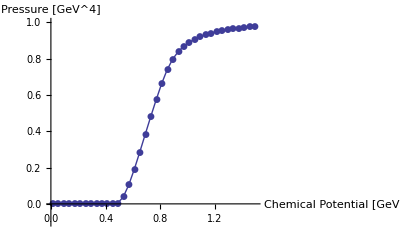

```mathematica
ListLinePlot[tablePressureZeroTNormalized,PlotStyle->PointSize[0.01],Joined->True,PlotMarkers->Automatic,AxesLabel->{"Chemical Potential [GeV]","Pressure [GeV^4]"},PlotRange->{{0,1.5},{-0.1,1}}]
```

Note que a mensagem de erro que aparece é devida aos cancelamentos sutis que devem acontecer para a integral abaixo do potencial quimico de limiar. Sendo que esperamos por razões físicas que a integral deve dar zero mesmo, eu não vejo motivo para não confiar nos cálculos.